```mathematica
Quit[]
```

## Load Packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities

### Functions for generating diagrams

```mathematica
(*exclusions=Join[{V[1],V[2],V[3],V[4]},mesonList];*)
exclusions={V[1],V[2],V[3](*,V[4]*)};

frModelName="EFT_MeV_DM_vector_no_contact";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateω=V[3];
statev=V[4];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Three body phase space bounds

```mathematica
getTBounds[s_,m1_,m2_,m3_,M_]:=Module[{E1,E2,t,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getSBounds⟦1⟧<s<getSBounds⟦2⟧}];
(* energies *)
E1=  (M^2+m1^2-s)/(2M);
E2= (M^2+m2^2-t)/(2M);
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,t]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}
]

getSBounds[m1_,m2_,m3_,M_]:={(m2+m3)^2,(M-m1)^2};


getYBounds[x_,m1_,m2_,m3_,M_]:=Module[{E1,E2,y,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getXBounds⟦1⟧<x<getXBounds⟦2⟧}];
(* energies *)
E1=  M x/ 2;
E2= M y/ 2;
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,y]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}]


getXBounds[m1_,m2_,m3_,M_]:={(M^2-(M-m1)^2+m1^2)/M^2,(M^2-(m2+m3)^2+m1^2)/M^2};
```

### FV dot

```mathematica
FVDot[fv1_,fv2_]:=fv1⟦1⟧fv2⟦1⟧-Dot[fv1⟦2;;4⟧,fv2⟦2;;4⟧];
```

## V→ l̄ l

### Compute Matrix Element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
PX={Q/2,0,0,(Q/2)√(1-4 μx^2)};
PXBAR={Q/2,0,0,-(Q/2)√(1-4 μx^2)};

PL={Q/2,√(1-z^2)(Q/2)√(1-4 μl^2),0,z(Q/2)√(1-4 μl^2)};

PLBAR={Q/2,-√(1-z^2)(Q/2)√(1-4 μl^2),0,-z(Q/2)√(1-4 μl^2)};
```

```mathematica
FVDot[PXBAR,PL]//FullSimplify
```

1/4 Q^2 (√(1-4 μl^2) √(1-4 μx^2) z+1)

```mathematica
SP[pl,pl]=FVDot[PL,PL];
SP[plbar,plbar]=FVDot[PLBAR,PLBAR];

SP[px,px]=FVDot[PX,PX];
SP[pxbar,pxbar]=FVDot[PXBAR,PXBAR];

SP[pl,plbar]=FVDot[PL,PLBAR];
SP[px,pxbar]=FVDot[PX,PXBAR];

SP[px,pl]=FVDot[PX,PL];
SP[px,plbar]=FVDot[PX,PLBAR];
SP[pxbar,pl]=FVDot[PXBAR,PL];
SP[pxbar,plbar]=FVDot[PXBAR,PLBAR];
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{statex,statexbar},{statel,statelbar}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {px,pxbar},
OutgoingMomenta-> {pl,plbar},
List-> False,
UndoChiralSplittings-> True,
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//ReplaceAll[#,ml-> μl*Q]&;
ampConj=ComplexConjugate[amp]//FCRenameDummyIndices;
msqrd = amp*ampConj//FermionSpinSum[#,ExtraFactor-> 1/4]&//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd = msqrd//ExpandScalarProduct//Simplify//Contract;
xxbarllbarγ`msqrd=msqrd//ReplaceAll[#,{ml-> μl*Q,mx-> μx*Q}]&//Simplify
]
```

(gvll^2 gvxx^2 Q^4 (4 μl^2+4 μx^2+(4 μl^2-1) (4 μx^2-1) z^2+1))/((mv-Q)^2 (mv+Q)^2)

```mathematica
xxbarllbarγ`σ=(2π)/(64 π^2 Q^2)((√(1-4 μl^2))/(√(1-4 μx^2)))Integrate[xxbarllbarγ`msqrd,{z,-1,1}]//ReplaceAll[#,{mv-> μv*Q}]&//FullSimplify
```

(gvll^2 gvxx^2 √(1-4 μl^2) (2 μl^2+1) (2 μx^2+1))/(12 π (μv^2-1)^2 √(1-4 μx^2) Q^2)

```mathematica
xxbarllbarγ`σ//ReplaceAll[#,{μl-> 0,μx-> 0}]&
```

(gvll^2 gvxx^2)/(12 π (μv^2-1)^2 Q^2)

## V→ l̄ l γ

### Compute Matrix element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[px,px]=μx^2*Q^2;
SP[pxbar,pxbar]=μx^2*Q^2;
SP[px,pxbar]=1/2 Q^2(1-2 μx^2);

SP[pl,pl]=μl^2*Q^2;
SP[plbar,plbar]=μl^2*Q^2;
SP[k,k]=0;

SP[pl,plbar]=1/2(s-2(μl*Q)^2);
SP[k,plbar]=1/2(t-(μl*Q)^2);
SP[k,pl]=1/2(u-(μl*Q)^2);
```

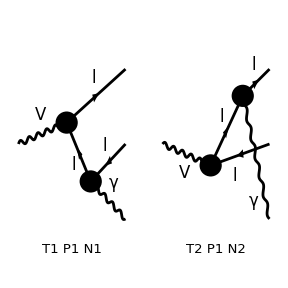

-1/((t-μl^2 Q^2)^2 (u-μl^2 Q^2)^2)4 gvll^2 qe^2 ((ḡ)^αμ (18 μl^8 Q^8-28 μl^6 Q^6 u+15 μl^4 Q^4 u^2+2 s^2 (t-μl^2 Q^2) (u-μl^2 Q^2)+t^3 (u-3 μl^2 Q^2)-3 μl^2 Q^2 u^3+3 t^2 (5 μl^4 Q^4-3 μl^2 Q^2 u)+2 s (-6 μl^6 Q^6+7 μl^4 Q^4 u+t^2 (u-2 μl^2 Q^2)-2 μl^2 Q^2 u^2+t (7 μl^4 Q^4-6 μl^2 Q^2 u+u^2))+t (-28 μl^6 Q^6+30 μl^4 Q^4 u-9 μl^2 Q^2 u^2+u^3))+2 (k̄)^α (4 μl^2 Q^2 (k̄)^μ (μl^2 Q^2-t) (μl^2 Q^2-u)+OverBar[pl]^μ (u-μl^2 Q^2) (-5 μl^4 Q^4+μl^2 Q^2 s+3 μl^2 Q^2 t+3 μl^2 Q^2 u-s t-t u)+OverBar[plbar]^μ (t-μl^2 Q^2) (-5 μl^4 Q^4+μl^2 Q^2 s+3 μl^2 Q^2 t+3 μl^2 Q^2 u-s u-t u))-2 OverBar[plbar]^α ((k̄)^μ (t-μl^2 Q^2) (5 μl^4 Q^4+s (u-μl^2 Q^2)+t (u-3 μl^2 Q^2)-3 μl^2 Q^2 u)+OverBar[pl]^μ (-10 μl^6 Q^6+11 μl^4 Q^4 u+2 s (t-μl^2 Q^2) (u-μl^2 Q^2)+t^2 (u-3 μl^2 Q^2)-3 μl^2 Q^2 u^2+t (11 μl^4 Q^4-8 μl^2 Q^2 u+u^2))-2 OverBar[plbar]^μ (t-μl^2 Q^2) (u-μl^2 Q^2)^2)-2 OverBar[pl]^α ((k̄)^μ (u-μl^2 Q^2) (5 μl^4 Q^4+s (t-μl^2 Q^2)+t (u-3 μl^2 Q^2)-3 μl^2 Q^2 u)+2 OverBar[pl]^μ (t-μl^2 Q^2)^2 (μl^2 Q^2-u)+OverBar[plbar]^μ (-10 μl^6 Q^6+11 μl^4 Q^4 u+2 s (t-μl^2 Q^2) (u-μl^2 Q^2)+t^2 (u-3 μl^2 Q^2)-3 μl^2 Q^2 u^2+t (11 μl^4 Q^4-8 μl^2 Q^2 u+u^2))))

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{statev},{statel,statelbar,stateγ}];

ampFA=CreateFeynAmp[diags];
Paint[diags,ColumnsXRows-> {2,1}];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {pv},
OutgoingMomenta-> {pl,plbar,k},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];
amp=ampFC//ReplaceAll[#,{ Pair[LorentzIndex[μ],Momentum[Polarization[pv,ⅈ]]]:> 1}]&;
amp=amp//PropagatorDenominatorExplicit//MomentumExpand;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd=amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd=msqrd//DoPolarizationSums[#,k,0]&//Contract//Simplify;
msqrd=msqrd//ReplaceAll[#,{ml-> μl*Q}]&;
xxbarllbarγ`Lμν=msqrd//Simplify
]
```

```mathematica
(xxbarllbarγ`Lμν) (FV[k,μ]+FV[pl,μ]+FV[plbar,μ])//Contract//ReplaceAll[#,u-> -s-t+Q^2+2 Q^2 μl^2]&//FullSimplify
```

0

```mathematica
Module[{amp,ampConj,msqrd},
amp=ⅈ gvxx SpinorVBar[pxbar,Q*μx].GA[μ].SpinorU[px,Q*μx];
ampConj=ComplexConjugate[ⅈ gvxx SpinorVBar[pxbar,Q*μx].GA[ν].SpinorU[px,Q*μx]];
msqrd=amp*ampConj//FermionSpinSum[#,ExtraFactor-> 1/4]&//ReplaceAll[#,DiracTrace-> Tr]&;
xxbarllbarγ`xμν=msqrd//Contract//FullSimplify]
```

1/2 gvxx^2 (Q^2 (-(ḡ)^μν)+2 OverBar[px]^ν OverBar[pxbar]^μ+2 OverBar[px]^μ OverBar[pxbar]^ν)

```mathematica
xxbarllbarγ`xμν(FV[px,μ]+FV[pxbar,μ])//Contract//Simplify
```

0

```mathematica
P[μ_]:=FV[px,μ]+FV[pxbar,μ];
```

```mathematica
xxbarllbarγ`xμν(P[μ]P[ν]-P[α]P[α]MT[μ,ν])//Contract//Simplify
```

gvxx^2 (2 μx^2+1) Q^4

### Convert to x and y

```mathematica
(xxbarllbarγ`L)=-(1/(3 Q^2))(xxbarllbarγ`Lμν)MT[μ,α]//Contract//Simplify;
xxbarllbarγ`Lμνxμν=gvxx^2(xxbarllbarγ`L)Q^4(1+2 μx^2);
xxbarllbarγ`dσdsdt=1/(2 Q^2 √(1-4 μx^2))1/(Q^4(1-μv^2)^2)1/(16 Q^2(2π)^3)xxbarllbarγ`Lμνxμν//ReplaceAll[#,{u-> -s-t+Q^2+2 Q^2 μl^2}]&;
xxbarllbarγ`dσdxdy=Q^4 xxbarllbarγ`dσdsdt//ReplaceAll[#,{s-> Q^2(1-x),t-> Q^2(1-y+μl^2)}]&//FullSimplify;

xxbarllbarγ`dσdxdy`dynamic=xxbarllbarγ`dσdxdy//SelectNotFree[#,y]&;
xxbarllbarγ`dσdxdy`coeff=xxbarllbarγ`dσdxdy//SelectFree[#,y]&;

xxbarllbarγ`dσdxdy-xxbarllbarγ`dσdxdy`dynamic*xxbarllbarγ`dσdxdy`coeff
```

0

```mathematica
(xxbarllbarγ`L)=(xxbarllbarγ`Lμν)MT[μ,α]//Contract//Simplify;
xxbarllbarγ`Lμνxμν=(xxbarllbarγ`L);
xxbarllbarγ`dσdsdt=xxbarllbarγ`Lμνxμν//ReplaceAll[#,{u-> -s-t+Q^2+2 Q^2 μl^2}]&;
xxbarllbarγ`dσdxdy=xxbarllbarγ`dσdsdt//ReplaceAll[#,{s-> Q^2(1-x),t-> Q^2(1-y+μl^2)}]&//FullSimplify;

xxbarllbarγ`dσdxdy`dynamic=xxbarllbarγ`dσdxdy//SelectNotFree[#,y]&;
xxbarllbarγ`dσdxdy`coeff=xxbarllbarγ`dσdxdy//SelectFree[#,y]&;

xxbarllbarγ`dσdxdy-xxbarllbarγ`dσdxdy`dynamic*xxbarllbarγ`dσdxdy`coeff
```

0

```mathematica
xxbarllbarγ`dσdxdy`dynamic//FullSimplify
xxbarllbarγ`dσdxdy`coeff
```

(4 μl^4 x^2+2 μl^2 (x^2 (3-2 y)-2 x (y-2) (y-1)+2 (y-1)^2)+(y-1) (x+y-1) (x^2+2 x (y-2)+2 (y-2) y+4))/((y-1)^2 (x+y-1)^2)

-(gvll^2 gvxx^2 (2 μx^2+1) qe^2)/(96 π^3 (μv^2-1)^2 √(1-4 μx^2) Q^2)

### Compute y integral

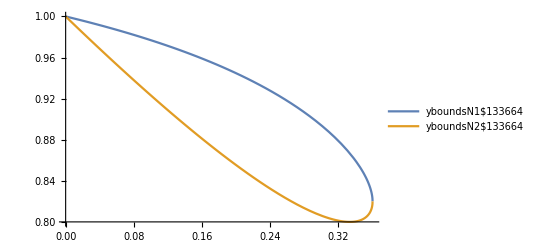

```mathematica
ybounds = getYBounds[x,0,μl*Q,μl*Q,Q]//Simplify;
xbounds=getXBounds[0,μl*Q,μl*Q,Q]//Simplify;

Module[{yboundsN1,yboundsN2,xboundsN1,xboundsN2},
(* test which curve is the upper and which is lower *)
yboundsN1=ybounds⟦1⟧/.{μl-> 0.4,Q->1};
yboundsN2=ybounds⟦2⟧/.{μl-> 0.4,Q->1};
xboundsN1=xbounds⟦1⟧/.{μl-> 0.4,Q->1};
xboundsN2=xbounds⟦2⟧/.{μl-> 0.4,Q->1};
Plot[{yboundsN1,yboundsN2},{x,xboundsN1,xboundsN2},PlotLegends->"Expressions"]
]
```

```mathematica
Module[{integral,lim1,lim2,result},
$Assumptions={xbounds⟦1⟧<x<xbounds⟦2⟧,μl>0};
integral=Integrate[xxbarllbarγ`dσdxdy`dynamic,y]//Simplify;
lim1=integral/.{y-> ybounds⟦1⟧};
lim2=integral/.{y-> ybounds⟦2⟧};
$Assumptions=True;
xxbarllbarγ`dσdx`dynamic=lim1-lim2//Simplify
]
```

1/x((x^2 (√(x-1) √(4 μl^2+x-1)-x+1))/(x-1)+(x^2 (√(x-1) √(4 μl^2+x-1)+x-1))/(x-1)+(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (-√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))+(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (√(x-1) √(4 μl^2+x-1)-x+1))/(2 (x-1)))-(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log(-(x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))-(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))+(8 μl^2 (2 μl^2+1) (x-1))/(-√(x-1) √(4 μl^2+x-1)+x-1)-(8 μl^2 (2 μl^2+1) (x-1))/(√(x-1) √(4 μl^2+x-1)+x-1))

```mathematica
xxbarllbarγ`dσdx`dynamic//SelectNotFree[#,Log[__]]&//SelectNotFree[#,Log[__]]&//StandardForm
```

(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]

Simply logs by hand

```mathematica
(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]
+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]
-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]
-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]
```

(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (-√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))

(-8 μl^4+x^2-2 (2 μl^2+1) x+2) log((x (√(x-1) √(4 μl^2+x-1)-x+1))/(2 (x-1)))

(8 μl^4-x^2+2 (2 μl^2+1) x-2) log(-(x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))

(8 μl^4-x^2+2 (2 μl^2+1) x-2) log((x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))

```mathematica
(((x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x)))/1)(((x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x)))/1)(1/(-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))))(1/((x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))))//Simplify//StandardForm
```

((1-x+√(-1+x) √(-1+x+4 μl^2))^2)/((-1+x+√(-1+x) √(-1+x+4 μl^2))^2)

```mathematica
xxbarllbarγ`dσdx`dynamic//StandardForm
```

1/x((8 (-1+x) μl^2 (1+2 μl^2))/(-1+x-√(-1+x) √(-1+x+4 μl^2))+(x^2 (1-x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)-(8 (-1+x) μl^2 (1+2 μl^2))/(-1+x+√(-1+x) √(-1+x+4 μl^2))+(x^2 (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))])

Compute put logs back in

```mathematica
xxbarllbarγ`dσdx`dynamic=1/x((8 (-1+x) μl^2 (1+2 μl^2))/(-1+x-√(-1+x) √(-1+x+4 μl^2))+(x^2 (1-x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)-(8 (-1+x) μl^2 (1+2 μl^2))/(-1+x+√(-1+x) √(-1+x+4 μl^2))+(x^2 (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(-1+x)+(2+x^2-8 μl^4-2 x (1+2 μl^2)) Log[((1-x+√(-1+x) √(-1+x+4 μl^2))^2)/((-1+x+√(-1+x) √(-1+x+4 μl^2))^2)])//FullSimplify
```

((2 √(4 μl^2+x-1) (x^2-4 μl^2 (x-1)-2 x+2))/(√(x-1))+(-8 μl^4-4 μl^2 x+(x-2) x+2) log(((√(x-1) √(4 μl^2+x-1)-x+1)^2)/((√(x-1) √(4 μl^2+x-1)+x-1)^2)))/x

### Compute Spectrum

```mathematica
4/96
```

1/24

Coefficient should be

```mathematica
8((qe^2 gvxx^2 gvll^2(1+2 μx^2))/(6 Q^4(1-μv^2)^2 √(1-4 μx^2)))(Q^2/(16(2π)^3))
```

(gvll^2 gvxx^2 (2 μx^2+1) qe^2)/(96 π^3 (1-μv^2)^2 √(1-4 μx^2) Q^2)

We computed coefficient to be

```mathematica
xxbarllbarγ`dσdxdy`coeff
```

-(gvll^2 gvxx^2 (2 μx^2+1) qe^2)/(96 π^3 (μv^2-1)^2 √(1-4 μx^2) Q^2)

```mathematica
(xxbarllbarγ`dσdxdy`coeff)/(xxbarllbarγ`σ)
```

-qe^2/(8 π^2 √(1-4 μl^2) (2 μl^2+1))

```mathematica
xxbarllbarγ`σ
xxbarllbarγ`dσdx`dynamic
xxbarllbarγ`dσdxdy`coeff
```

(gvll^2 gvxx^2 √(1-4 μl^2) (2 μl^2+1) (2 μx^2+1))/(12 π (μv^2-1)^2 √(1-4 μx^2) Q^2)

((2 √(4 μl^2+x-1) (x^2-4 μl^2 (x-1)-2 x+2))/(√(x-1))+(-8 μl^4-4 μl^2 x+(x-2) x+2) log(((√(x-1) √(4 μl^2+x-1)-x+1)^2)/((√(x-1) √(4 μl^2+x-1)+x-1)^2)))/x

-(gvll^2 gvxx^2 (2 μx^2+1) qe^2)/(96 π^3 (μv^2-1)^2 √(1-4 μx^2) Q^2)

```mathematica
xxbarllbarγ`dndx=xxbarllbarγ`dσdx`dynamic*(xxbarllbarγ`dσdxdy`coeff/xxbarllbarγ`σ)//FullSimplify
```

-(qe^2 ((2 √(4 μl^2+x-1) (x^2-4 μl^2 (x-1)-2 x+2))/(√(x-1))+(-8 μl^4-4 μl^2 x+(x-2) x+2) log(((√(x-1) √(4 μl^2+x-1)-x+1)^2)/((√(x-1) √(4 μl^2+x-1)+x-1)^2))))/(4 π^2 √(1-4 μl^2) (2 μl^2 x+x))

```mathematica
xxbarllbarγ`dndx//ReplaceAll[#,{μl-> mul,μx-> mux}]&//FortranForm
```

-(qe**2*((2*Sqrt(-1 + 4*mul**2 + x)*(2 - 4*mul**2*(-1 + x) - 2*x + x**2))/Sqrt(-1 + x) + 
     -       (2 - 8*mul**4 - 4*mul**2*x + (-2 + x)*x)*Log((1 - x + Sqrt(-1 + x)*Sqrt(-1 + 4*mul**2 + x))**2/(-1 + x + Sqrt(-1 + x)*Sqrt(-1 + 4*mul**2 + x))**2)))/
     -  (8.*Sqrt(1 - 4*mul**2)*(1 + 3*mul**2 - mux**2)*Pi**2*x)

```mathematica
Clear[spec]
```

```mathematica
spec[egam_,Q_]:=2/Q xxbarllbarγ`dndx//ReplaceAll[#,{μl-> 105.6583715/Q,μx-> 200./Q,μv-> 3000./Q,qe-> 0.30281770035689687}]&//ReplaceAll[#,x-> 2.egam/Q]&
```

```mathematica
spec[10,1000.]
```

0.00161716+0. ⅈ

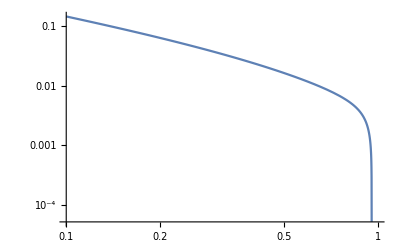

```mathematica
LogLogPlot[spec[x],{x,0.1,1}]
```

```mathematica
(spec[10.,1000.]-0.0015914203375067375)/spec[10.,1000.]*100
```

1.59158+0. ⅈ